## Planar Fragmentation

Use WFR in the future. Now load Lib:

```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["Planar.wl"]
```

Use the WFR, however it seems slower to use resource function than to use local defined function.

```mathematica
PlanarPolygonFragmentation=ResourceFunction["PlanarPolygonFragmentation"];
```

## Depict Tile

### General Tile

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[(If[ref,{-#[[1]], #[[2]]}, #] & /@ ( basicVertices - Threaded[basicVertices[[pt]]] ) ) + Threaded[or]]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

### Hat Tile

```mathematica
vertexAngles=<|1->3/4,2->1/3,3->1/4,4->1/3,5->3/4,6->1/3,7->1/4,8->2/3,9->1/4,10->2/3,11->1/4,12->1/3,13->1/2,14->1/3|>;
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
oneFourthVertices=Keys[Select[vertexAngles,#==1/4&]];
```

```mathematica
oneThirdVertices=Keys[Select[vertexAngles,#==1/3&]];
```

```mathematica
oneHalfVertices=Keys[Select[vertexAngles,#==1/2&]];
```

```mathematica
twoThirdVertices=Keys[Select[vertexAngles,#==2/3&]];
```

```mathematica
threeFourthVertices=Keys[Select[vertexAngles,#==3/4&]];
```

## Cluster Function

### Tiles Polygons

```mathematica
H2poly=;
H1poly=;
```

```mathematica
H8poly=Polygon[];
H7poly=Polygon[];
```

```mathematica
AH7superPoly=;
H8superPoly=;
```

```mathematica
metaTile[pos_,dir_:0,pt_,choice_:True]:=With[{
vertices=If[
TrueQ[choice],
.Transpose@RotationMatrix[dir*Pi/6],
.Transpose@RotationMatrix[dir*Pi/6]
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
cluster[pos_,dir_:0,pt_,choice_:False]:=With[{
vertices=If[
TrueQ[choice],
.Transpose@RotationMatrix[dir*Pi/6],
.Transpose@RotationMatrix[dir*Pi/6]
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
angleVertices[angle_][poly_]:=First/@Position[PolygonAngle[poly],_?(#==2Pi*angle&),{1}]
```

```mathematica
angleToPointsBuildFunction=Function[
{choice,tileFunction},
angleToPoints[ToString[tileFunction]][choice]=Association[#->Join@@Position[
RegionMember[
tileFunction[{0,0},0,1,choice],
CirclePoints[First[tileFunction[{0,0},0,1,choice]][[#]],{1/4,Pi/12},12]
],True
]&/@Range[Length[First[tileFunction[{0,0},0,1,choice]]]]]
];
```

### Tile Vertices

```mathematica
standardH8Vertices=;
```

```mathematica
standardH7Vertices=;
```

```mathematica
clusterVertices[pos_,dir_:0,pt_,choice_:False]:=With[{
	vertices=If[
		TrueQ[choice],
			standardH8Vertices . Transpose[RotationMatrix[dir*Pi/6]],
			standardH7Vertices . Transpose[RotationMatrix[dir*Pi/6]]
		]
	},
	vertices+Threaded[pos-vertices[[pt]]]
]
```

```mathematica
clusterInnerVertices[pos_, dir_:0, pt_, False] :=  . Transpose[RotationMatrix[dir*Pi/6]] + Threaded[clusterVertices[pos,dir,pt,False][[1]]]
```

```mathematica
clusterInnerVertices[pos_, dir_:0, pt_, True] :=  . Transpose[RotationMatrix[dir*Pi/6]] + Threaded[clusterVertices[pos,dir,pt,True][[1]]]
```

```mathematica
canonicalCluster[code_]:={First[clusterVertices[##]],#2,1,#4}&@@code;
```

### Project Tiles Code

```mathematica
metaTileCode[pos_,dir_:0,pt_,False]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@
]
```

```mathematica
metaTileCode[pos_,dir_:0,pt_,True]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@{{{0,0},0,False,1}}
]
```

```mathematica
clusterCode[pos_,dir_,pt_,False]:=With[
{H7vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H7vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

```mathematica
clusterCode[pos_,dir_,pt_,True]:=With[
{H8vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H8vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

### angle information

```mathematica
angleToPoints["metaTile"][True]=;
angleToPoints["metaTile"][False]=;
```

```mathematica
angleToPoints["cluster"][True]=;
angleToPoints["cluster"][False]=;
```

```mathematica
getPointsOccupation[tileFunction_][dir_,pt_,choice_]:=Mod[#+dir,12,1]&/@(pt/.angleToPoints[ToString[tileFunction]][choice])
```

### intersectingQ

```mathematica
intersectingQ[p1_Polygon,p2_Polygon,dimension_Integer:10]:=With[{res=PlanarPolygonFragmentation[p1,p2,"BinCount"->dimension]},If[res==={}||Total[Length/@res]==3,False,True]]
intersectingQ[ps_List,dimension_Integer:10]:=Fold[
If[
#1===False,
False,
With[{res=PlanarPolygonFragmentation[#1,#2,"BinCount"->dimension]},
If[Total[Length/@res]==3,SortBy[res,Length][[1,1]],False]
]
]&,
ps
]
```

### all rotations

```mathematica
allRotations=Function[r,Sort[Apply[{Mod[#1+r,12],#2,#3}&,#,{1}]]]/@Range[0,11]&;
```

## Vertex information

### Hat vertex configuration

```mathematica
oneThirdAndTwoThirdList=;
oneThirdList=;
```

### Cluster vertex information

```mathematica
vertexClass[True]=Association[
MapIndexed[
First[#2]->Lookup[(Merge[Association[MapIndexed[#1->#2&,hatVertices@@#]]&/@,Join@@#&]),Key[#1]]&,
First[cluster[{0,0},10,1,True]]
]
];
vertexClass[False]=Association[
MapIndexed[
First[#2]->Lookup[(Merge[Association[MapIndexed[#1->#2&,hatVertices@@#]]&/@,Join@@#&]),Key[#1]]&,
First[cluster[{0,0},10,1,False]]
]
];
```

```mathematica
clusterVertexAngles[True]=;
clusterVertexAngles[False]=;
oneThirdClusterVertex[True]={2,4,10,12,16,18,20,30,32,36,38,42};
oneThirdClusterVertex[False]={2,4,10,12,16,18,20,22,30,32,34,38,40,44};
twoThirdClusterVertex[True]={6,8,14,22,24,26,28,34,40};
twoThirdClusterVertex[False]={6,8,14,24,26,28,36,42};
```

## Quick Visualize

```mathematica
Options[visualize]={"ChooseColor" -> {Lighter@Blue, Lighter@Red}};
visualize[code_List, opt : OptionsPattern[]]:=Graphics[
{
	OptionValue["ChooseColor"][[1]],EdgeForm[Darker@OptionValue["ChooseColor"][[1]]],Opacity[.5],
	cluster@@@Select[code,MemberQ[True]],
	OptionValue["ChooseColor"][[2]],EdgeForm[Darker@OptionValue["ChooseColor"][[2]]],Opacity[.5],
	cluster@@@Select[code,MemberQ[False]]
}];
```

## Graph Function

```mathematica
depthNode[n_Integer][g_Graph]:=Select[VertexList[g],GraphDistance[g,First@VertexList[g],#]==n&];
leaves[g_Graph]:=Select[VertexList[g],VertexOutDegree[g,#]==0&]
```

# Main

## Generate Cases From Hat Tile Vertex Configuration

```mathematica
validVF13=oneThirdList[[All,All,3]];
validVF1323=Union@@(#[[All,All,3]]&/@{oneThirdAndTwoThirdList,oneThirdList});
```

```mathematica
allOneThirdStatesForOne=Join@@(Tuples[{Range[0,11],oneThirdClusterVertex[#],{#}}]&/@{True,False});
allTwoThirdStatesForOne=Join@@(Tuples[{Range[0,11],twoThirdClusterVertex[#],{#}}]&/@{True,False});
allOneThirdStatesForOne//Length
allTwoThirdStatesForOne//Length
```

312

204

```mathematica
classifiedByVertexAndPoints=GroupBy[
Join[allOneThirdStatesForOne,allTwoThirdStatesForOne],
{Sort[getPointsOccupation[cluster]@@#]&,Sort[#[[2]]/.vertexClass[#[[3]]]]&}
];
```

```mathematica
cases1323=DeleteDuplicates[Join@@Apply[
Tuples[{
Lookup[Lookup[classifiedByVertexAndPoints,Key[{1,2,3,4,5,6,7,12}],{}],Key[Sort[#2]],{}],
Lookup[Lookup[classifiedByVertexAndPoints,Key[{8,9,10,11}],{}],Key[Sort[#1]],{}]
}]&,
{{#1},{##2}}&@@@(Join@@(Permutations/@validVF1323)),
{1}
]];
cases1323//Length
```

233

```mathematica
cases13=Join@@(Tuples[{
Lookup[Lookup[classifiedByVertexAndPoints,Key[{1,2,3,4}],{}],Key[{#1}],{}],
Lookup[Lookup[classifiedByVertexAndPoints,Key[{5,6,7,8}],{}],Key[{#2}],{}],
Lookup[Lookup[classifiedByVertexAndPoints,Key[{9,10,11,12}],{}],Key[{#3}],{}]
}]&@@@validVF13);
cases13=DeleteDuplicatesBy[Sort@*allRotations][cases13];
cases13//Length
```

544

```mathematica
Timing[res1=Select[cases1323,intersectingQ[cluster[{0,0},##]&@@@#,15]=!=False&];]
```

{10.4219,Null}

```mathematica
Timing[res2=Select[cases13,intersectingQ[cluster[{0,0},##]&@@@#,15]=!=False&];]
```

{45.6094,Null}

```mathematica
res1//Length
res2//Length
```

186

164

```mathematica
res1=With[{dir=#[[1,1]]},({Mod[#1-dir,12],#2,#3}&@@@#)]&/@res1;
res2=With[{dir=#[[1,1]]},({Mod[#1-dir,12],#2,#3}&@@@#)]&/@res2;
```

```mathematica
Iconize/@{res1,res2}
```

{,}

## Reduce Vertex Configuration Space (1)

### Initial configuration list

```mathematica
configuration1323=;
configuration13=;
```

### Vertex configuration functions

```mathematica
vertexConfiguration[code_]:=Block[{vf=Association[]},
Scan[
Function[tile,
MapThread[If[KeyExistsQ[vf,#1],
AppendTo[vf[#1],#2->tile],
AssociateTo[vf,#1->{#2->tile}]
]&,
{
First[cluster@@tile][[
Join[oneThirdClusterVertex[Last[tile]],twoThirdClusterVertex[Last[tile]]]
]],
Join[oneThirdClusterVertex[Last[tile]],twoThirdClusterVertex[Last[tile]]]
}
]
],
code
];
vf
]
```

```mathematica
vertexValidQ[vertexConfg_,configurationList_]:=With[{res=Catch[
Scan[
If[
Or@@(Function[r,SubsetQ[{Mod[#1+r,12],#2,#3}&@@@#,vertexConfg]]/@Range[0,11]),
Throw[True]
]&,
configurationList
]]},
TrueQ[res]
]
```

```mathematica
getInvalidVertices[configurationList_]:=Cases[
KeyValueMap[
#1->vertexValidQ[{#[[2,2]],#[[1]],#[[2,4]]}&/@#2,configurationList]&,
Select[vertexConfiguration[#],Length[#]>1&]
],(pos_->False):>pos
]&;
```

### Eliminate until fixed:

```mathematica
res=Block[
{
eliminatedCasesRecord=<||>,
invalidVerticesForEachCase,
eliminationProcess
},
eliminationProcess=FixedPointList[
Function[{twoLists},
invalidVerticesForEachCase=getInvalidVertices[Join@@twoLists]/@Map[Prepend[#,{0,0}]&,#,{2}]&/@twoLists;
Function[n,
With[{pts=invalidVerticesForEachCase[[n]][[#]],case=twoLists[[n]][[#]]},If[
Length[pts]==0,case,
AssociateTo[eliminatedCasesRecord,case->pts];Nothing
]]&/@Range[Length[invalidVerticesForEachCase[[n]]]]
]/@{1,2}
],
{configuration13,configuration1323}
];
<|
"eliminationProcess"->eliminationProcess,
"eliminatedCasesRecord"->eliminatedCasesRecord
|>
];//Timing
```

{237.031,Null}

```mathematica
Map[Length,res["eliminationProcess"],{2}]
```

{{164,186},{56,157},{20,103},{15,94},{15,94}}

```mathematica
Iconize/@res["eliminationProcess"][[-1]]
```

{,}

### Visualize invalid cases and its invalid points

```mathematica
KeyValueMap[
Graphics[
{
EdgeForm[Black],
Lighter@Blue,Opacity[.6],
cluster@@@(Prepend[#,{0,0}]&/@#1),
Opacity[1],Red,Disk[#2,.5]
}
]&,
res["eliminatedCasesRecord"]
]//Partition[#,UpTo[11]]&//Grid
```

## Reduce Vertex Configuration Space (2)

### Group 1/3+2/3 by co-join part

```mathematica
codes=Map[Prepend[#,{0,0}]&,,{2}];
```

```mathematica
groups=KeySortBy[Sort@*Last][GroupBy[codes,
Sort[Sort/@Values[{#[[1]],#[[2,4]]}&/@#&/@Select[vertexConfiguration[#],Length[#]>=2&]]]&
]];
groups//Length
```

29

Only need to select representatives from echo group.

```mathematica
representatives=Values[groups[[All,1]]];
```

```mathematica
visualize/@representatives//Partition[#,UpTo[10]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

### Set vertex configuration lists

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=;
```

### Grow function implementation

#### Cluster 1/3 and 2/3 points information

```mathematica
clusterPointsInformation[code_] := Block[{
	inf=<||>
},
	Scan[
		Function[tileCode,
			MapThread[
				If[
					KeyExistsQ[inf,#1],
					AppendTo[inf[#1],#2->tileCode],
					AssociateTo[inf,#1->{#2->tileCode}]
				]&,
				{
					Part[
						First[cluster@@tileCode],
						Join[oneThirdClusterVertex[Last[tileCode]],twoThirdClusterVertex[Last[tileCode]]]
					],
					Join[oneThirdClusterVertex[Last[tileCode]],twoThirdClusterVertex[Last[tileCode]]]
				}
			]
		],
		code
	];
	inf
];
```

#### Build Cluster Tiling State

```mathematica
clusterTilingState[code_]:=<|"code"->code,
	"boundaryPoints" -> Select[
		clusterPointsInformation[code],
		Total[Lookup[clusterVertexAngles[Last[#2]], #1]& @@@ #] <1 &]
	|>;
```

#### Pattern Match Generator

```mathematica
generatorH8[boundaryPointsInf_]:=Block[{
	allPossibleConfigurations = Transpose[
		Function[r,
			Apply[
				{ Mod[#1+r,12], #2, #3}&,
				Join[oneThirdTheoremListCluster, oneThirdAndTwoThirdTheoremListCluster],
			{2}]
		] /@ Range[0,11]
	],
	pointsBranches
},
	pointsBranches = With[
	{
		canonicalInf=Map[{#[[2,2]],#[[1]],#[[2,4]]}&,boundaryPointsInf,{2}]
	},
		Association[
			KeyValueMap[
				Function[{pt,conf}, pt -> Map[Prepend[#,pt]&, conf, {2}]]
				,
				Association[
					KeyValueMap[
						Function[{pt,conf},
							pt -> DeleteDuplicatesBy[
							(If[
								SubsetQ[#,conf],
								Complement[#,conf],
								Nothing
							]& /@ (Join @@ allPossibleConfigurations)), Sort]
						],
						canonicalInf
					]
				]
			]
		]
	];
	pointsBranches
]
```

#### Main Grow Function

```mathematica
Options[growH8Tiling] = {branchNumLimit -> Infinity, ChoosePoints -> False};
growH8Tiling[state_, opt:OptionsPattern[]]:=Block[
{
	pointsBranches = generatorH8[
		Select[
			If[
				OptionValue[ChoosePoints] =!= False,
				KeySelect[state["boundaryPoints"], MemberQ[OptionValue[ChoosePoints], #]&],
				state["boundaryPoints"]
			],
			Total[Lookup[clusterVertexAngles[Last[#2]], #1, {}]& @@@ #] <1 &]
		],
	intersectionTestFunction,
	boundaryTiles = DeleteDuplicates[Join @@ Values[state["boundaryPoints"]][[All,All,2]]],
	boundaryPoints,
	innerPoints
},
	
	If[Length[pointsBranches]===0,Return[{}]];
	
	With[
		{invalidVertices = Keys[Select[pointsBranches, Length[#]==0&]]},
		If[
			Length[invalidVertices] > 0,
			Sow[invalidVertices];
			Print["invalid Vertices:", invalidVertices];
			Return[{}]
		]
	];
	
	boundaryPoints = Union @@ (clusterVertices @@@ boundaryTiles);
	
	innerPoints = Join @@ (clusterInnerVertices @@@ boundaryTiles);
	
	intersectionTestFunction=Function[newCode,
		With[{
			newBoundaryPoints=Union@@(clusterVertices@@@newCode),
			newInnerPoints=Join@@(clusterInnerVertices@@@newCode)
		},
		If[
			IntersectingQ[boundaryPoints,newInnerPoints]||
			IntersectingQ[newBoundaryPoints,innerPoints]||
			IntersectingQ[newInnerPoints,innerPoints],
			Nothing,
			newCode
		]
		]
	];
	
	pointsBranches = GroupBy[
		Map[intersectionTestFunction, Select[pointsBranches, Length[#] <= OptionValue[branchNumLimit]& ], {2}],
	Length];
	
	If[
		KeyExistsQ[pointsBranches, 0],
			With[
			{impossibleVertices = Keys[pointsBranches[0]]},
			If[
				Length[impossibleVertices]>0,
				Sow[impossibleVertices];
				Print["impossible Vertices:",impossibleVertices];
				Return[{}]
			]
		]
	];
	
	If[
		KeyExistsQ[pointsBranches,1],
		
		{clusterTilingState[Join[state["code"], DeleteDuplicatesBy[canonicalCluster][Join@@(Join@@pointsBranches[1])]]]},
		
		clusterTilingState[Join[state["code"], #]]& /@ First[
				TakeSmallestBy[
					First[KeySort[pointsBranches]]
				,
				- Count[#[[All, All, 4]], False, {2}]&,
				1
				]
			]
	]
]
```

### Eliminate by testing impossible vertices

#### 29 to 19

Grow one generation, is equivalent to test if there is any impossible vertices on the boundary:

```mathematica
invalidRepresentatives=With[{
res=Reap[growH8Tiling[clusterTilingState[#]]]
},
If[Length[res[[2]]]!=0,#->res[[2,1,1]],Nothing]
]&/@representatives;//Timing
```

impossible Vertices:{{0,-2 √3},{1,5 √3},{0,6 √3},{-2,-2 √3},{3,5 √3},{2,-2 √3},{3,-3 √3},{5,5 √3}}

impossible Vertices:{{3,5 √3},{2,-2 √3},{3,-3 √3},{5,5 √3}}

impossible Vertices:{{-3,-5 √3},{-2,2 √3},{-3,3 √3},{-5,-5 √3},{-1,√3}}

impossible Vertices:{{0,-2 √3},{-2,-2 √3}}

impossible Vertices:{{-1,√3}}

impossible Vertices:{{4,2 √3},{5,3 √3}}

impossible Vertices:{{3,√3},{-3,-3 √3},{-4,-4 √3},{2,0},{-1,-√3},{-2,-2 √3},{-5,-3 √3},{-4,-2 √3},{1,√3},{2,2 √3},{-5,-√3},{-4,0},{-2,0},{1,3 √3}}

impossible Vertices:{{-4,0},{-2,0}}

impossible Vertices:{{4,2 √3},{3,√3},{1,√3},{-2,-4 √3},{-7,-5 √3},{-6,-4 √3},{-4,-4 √3},{-1,√3}}

impossible Vertices:{{-8,0},{-7,-√3}}

{42.2656,Null}

Visualize outlaw cases and their outlaw points:

```mathematica
Show[visualize[#1],Graphics[{EdgeForm[Black],Red,Disk[#2,.3]}]]&@@@invalidRepresentatives//Partition[#,5]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
groups=Select[groups,!MemberQ[invalidRepresentatives[[All,1]],#[[1]]]&];
groups//Length
```

19

```mathematica
Iconize[groups]
```

#### Set Vertex configuration lists

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=(Join@@Values[])[[All,All,2;;]];
```

#### 19 to 18:

Grow one generation, is equivalent to test if there is any impossible vertices on the boundary:

```mathematica
groups=;
representatives=Values[groups[[All,1]]];
```

```mathematica
invalidRepresentatives=With[{
res=Reap[growH8Tiling[clusterTilingState[#]]]
},
If[Length[res[[2]]]!=0,#->res[[2,1,1]],Nothing]
]&/@representatives;//Timing
```

impossible Vertices:{{-4,0},{-2,0}}

{19.4844,Null}

Visualize outlaw cases and their outlaw points:

```mathematica
Show[visualize[#1],Graphics[{EdgeForm[Black],Red,Disk[#2,.3]}]]&@@@invalidRepresentatives//Partition[#,UpTo@5]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
groups=Select[groups,!MemberQ[invalidRepresentatives[[All,1]],#[[1]]]&];
groups//Length
```

18

```mathematica
Iconize[groups]
```

### Update vertex configuration list

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=(Join@@Values[])[[All,All,2;;]];
```

### Record vertex configuration list

Previous result

```mathematica
Iconize/@{oneThirdTheoremListCluster,oneThirdAndTwoThirdTheoremListCluster}
```

{,}

## Reduce By growing

### Eliminate two cases in 1/3 v.f.

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=;
```

```mathematica
codes=Map[Prepend[#,{0,0}]&,oneThirdTheoremListCluster[[{12,13}]],{2}];
```

```mathematica
gs=Reap[NestGraph[growH8Tiling,clusterTilingState@#,5]]&/@codes;//Timing
```

impossible Vertices:{{18,4 √3},{14,4 √3},{12,4 √3},{16,4 √3},{16,2 √3},{18,2 √3},{14,2 √3},{-15,7 √3},{-13,5 √3},{-12,4 √3},{-14,6 √3},{-11,7 √3},{-12,8 √3},{-10,6 √3},{-3,-11 √3},{-1,-9 √3},{0,-8 √3},{-2,-10 √3},{-5,-9 √3},{-6,-10 √3},{-4,-8 √3}}

impossible Vertices:{{6,-4 √3},{5,-5 √3}}

{7.125,Null}

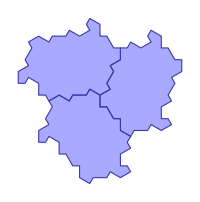
-Graphics-→-Graphics- | -Graphics-

```mathematica
Grid[{{
Row[
Show[#,ImageSize->200]&/@{
visualize[codes[[1]]],Show[visualize[VertexList[gs[[1,1]]][[-1]]["code"]],
Graphics[{EdgeForm[Black],Red,Disk[gs[[1,2,1,1]],.5]}]]
},Style["→",Red,30]]
,
Show[visualize[codes[[2]]],Graphics[{EdgeForm[Black],Red,Disk[gs[[2,2,1,1]],.5]}]]
}
},Frame->All,FrameStyle->LightGray
]
```

### Update vertex configuration list

```mathematica
DeleteCases[oneThirdTheoremListCluster,Alternatives@@(codes[[All,All,2;;]])]//Iconize
```

### Eliminate 1/3+2/3

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=;
```

```mathematica
codes=Map[Prepend[#,{0,0}]&,oneThirdAndTwoThirdTheoremListCluster,{2}];
```

```mathematica
groups=KeySortBy[Sort@*Last][GroupBy[
codes,Sort[Sort/@Values[{#[[1]],#[[2,4]]}&/@#&/@Select[vertexConfiguration[#],Length[#]>=2&]]]&]];
groups//Length
```

18

```mathematica
representatives=Values[groups[[All,1]]];
```

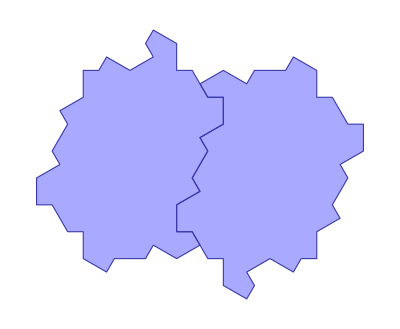
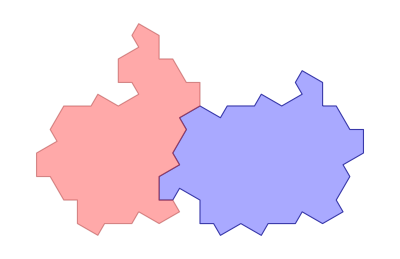
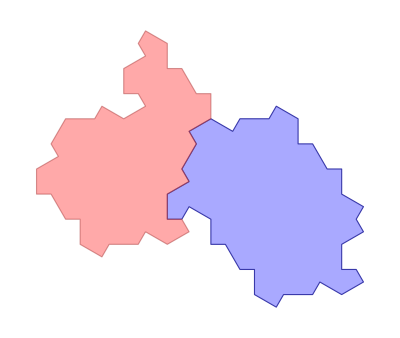
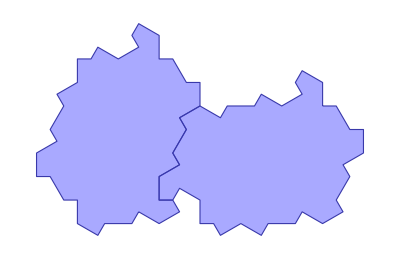
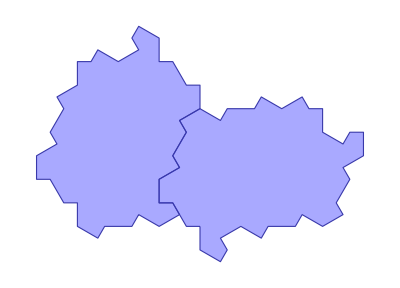
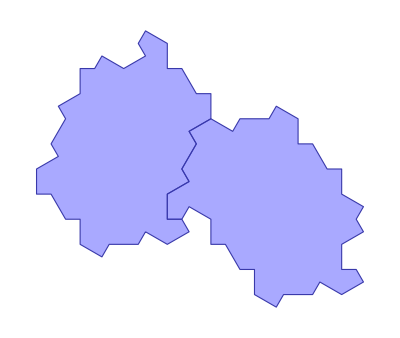
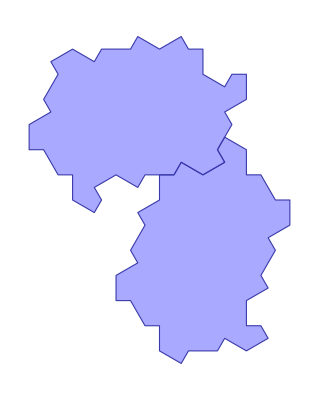
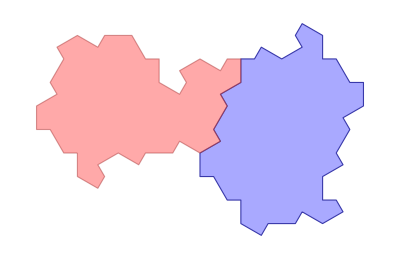

```mathematica
visualize/@representatives//Row
```

Only the first group is invalid (known from previous trying).

```mathematica
g=Reap[NestGraph[growH8Tiling,clusterTilingState[representatives[[1]]],60]];//Timing
```

invalid Vertices:{{-9,5 √3}}

invalid Vertices:{{12,-2 √3}}

impossible Vertices:{{-30,8 √3},{-28,8 √3},{-32,4 √3},{-31,7 √3},{-33,5 √3},{-32,6 √3},{-27,√3},{-29,5 √3},{-30,4 √3},{-28,2 √3},{-27,7 √3},{-28,6 √3},{-29,3 √3}}

impossible Vertices:{{-26,-8 √3},{-31,-9 √3},{-33,-9 √3},{-27,-9 √3},{-29,-9 √3},{-35,-7 √3},{-36,-6 √3},{-34,-8 √3},{-39,-√3},{-37,-3 √3},{-36,-4 √3},{-38,-2 √3}}

impossible Vertices:{{-52,-28 √3},{-54,-28 √3},{-50,-28 √3},{-54,-30 √3},{-52,-30 √3},{-51,-29 √3},{-49,-29 √3}}

{481.641,Null}

The growth tree is finite:

```mathematica
SelectFirst[Range[60,1,-1],Length[depthNode[#][g[[1]]]]!=0&]
```

51

Visualize all dead ends:

```mathematica
MapThread[
Show[visualize[#1["code"]],
Graphics[{EdgeForm[Black],Red,Disk[#2,1]}]
]&,
{
leaves[g[[1]]],
g[[2,1]]
}]//List//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
groups=groups[[2;;]];
Iconize[groups]
```

### Update vertex configuration list:

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=(Join@@Values[])[[All,All,2;;]];
```

### Eliminate super-{6,6,6} (20,20,20)

```mathematica
superSymmetric={{{0,0},0,20,True},{{0,0},4,20,True},{{0,0},8,20,True}};
```

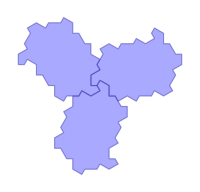

```mathematica
Show[visualize[superSymmetric],ImageSize->200]
```

```mathematica
g0=Reap[NestGraph[growH8Tiling,clusterTilingState[superSymmetric],60]];//Timing
```

invalid Vertices:{{-18,-26 √3},{48,4 √3},{-30,22 √3}}

{44.8125,Null}

Visualize growth process and eventual dead end:

```mathematica
Append[visualize[#["code"]]&/@VertexList[g0[[1]]][[;;-2]],
Show[
visualize[VertexList[g0[[1]]][[-1]]["code"]],
Graphics[{EdgeForm[Black],Red,Disk[g0[[2,1,1]],1.5]}]
]
]//Partition[#,UpTo[6]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
DeleteCases[oneThirdTheoremListCluster,superSymmetric[[All,2;;]]]//Iconize
```

## Final Vertex Configuration

```mathematica
oneThirdTheoremListCluster=;
oneThirdAndTwoThirdTheoremListCluster=;
```

```mathematica
groups=KeySortBy[Sort@*Last][GroupBy[oneThirdAndTwoThirdTheoremListCluster,
Sort[Sort/@Values[{#[[1]],#[[2,4]]}&/@#&/@Select[vertexConfiguration[Prepend[#,{0,0}]&/@#],Length[#]>=2&]]]&
]];
groups//Length
```

17

### 1/3

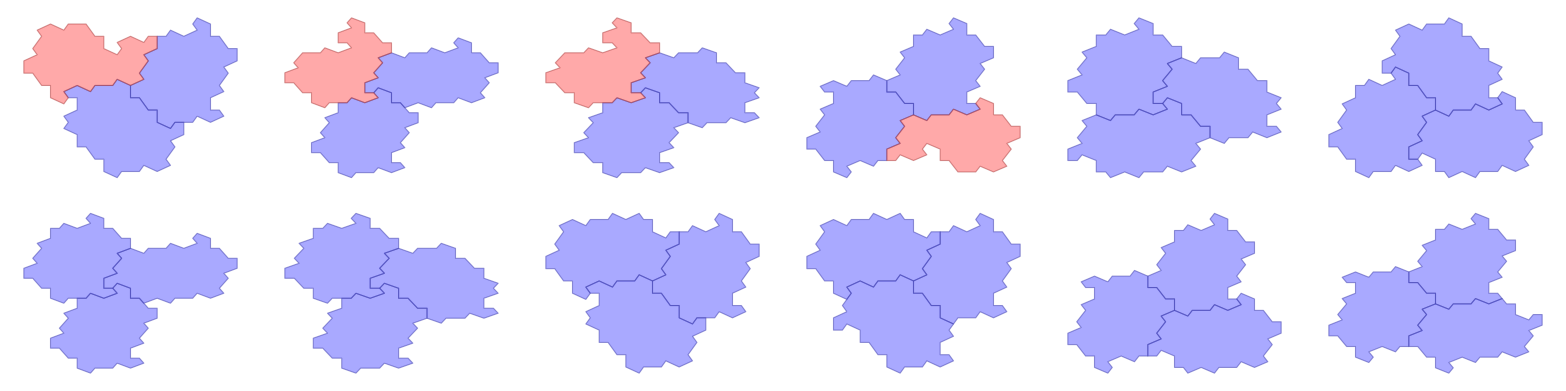

```mathematica
visualize[Prepend[#,{0,0}]&/@#]&/@SortBy[Last/@#&]@oneThirdTheoremListCluster//Partition[#,6]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

### 1/3 + 2/3

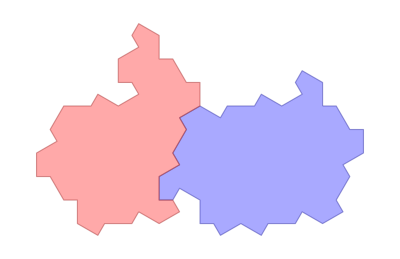
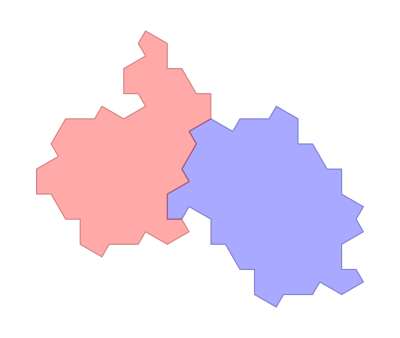
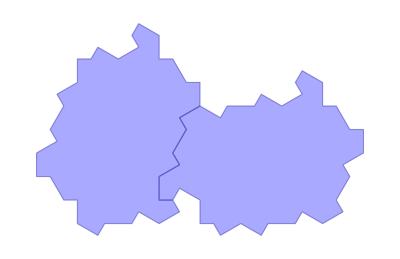
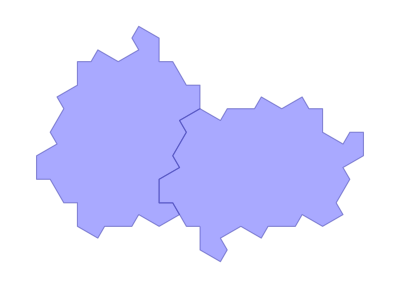
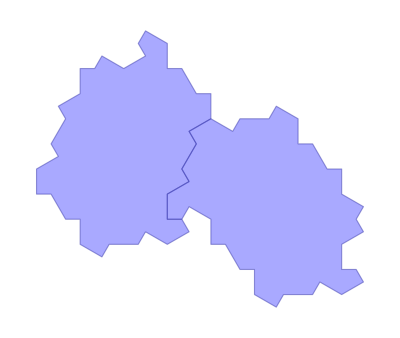
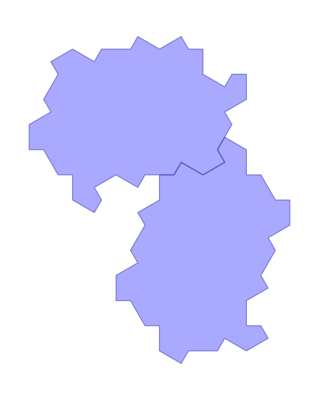
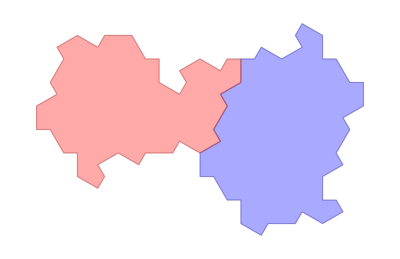
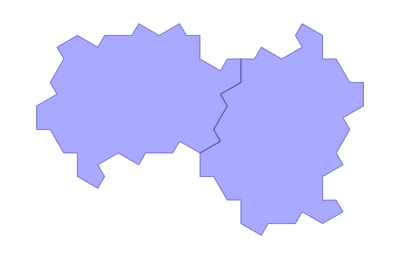
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
visualize[Prepend[#,{0,0}]&/@#]&/@Values[groups[[All,1]]]//Partition[#,UpTo@9]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```